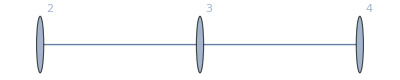

```mathematica
Graph[{1<->2,2<->3}, VertexLabels -> Table[i->i+1,{i,3}]]
```

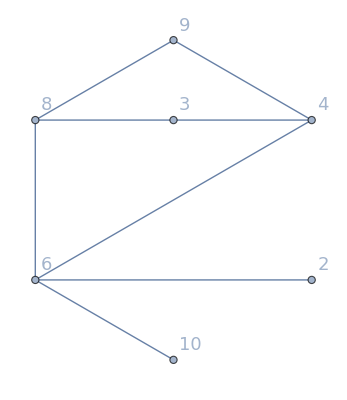

Set::write: Tag Inherited in Inherited[State] is Protected.

```mathematica
PlanarGraph[{1 <-> 2, 1 <-> 4, 2 <-> 3, 3 <-> 4, 2 <-> 5, 4 <-> 5, 5 <-> 6, 5 <-> 7}, VertexLabels -> {1 -> 9, 2 -> 4, 3 -> 3, 4 -> 8, 5 -> 6, 6 -> 2, 7 -> 10}, VertexLabelStyle->18, VertexSize->0.07]
```

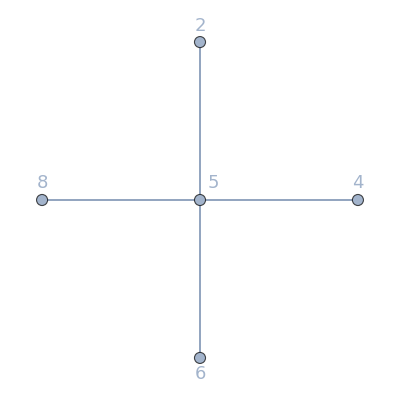

```mathematica
Graph[{3<-> 1, 2 <-> 1, 4 <-> 1, 5 <-> 1}, VertexLabels -> {1 -> 5, 2->Placed[4, Above],3 -> Placed[2,Above],4->Placed[6,Below], 5 -> Placed[8,Above]}, VertexLabelStyle->18,  VertexCoordinates->{{0,1},{0,0},{1,0}, {0,-1},{-1,0}}, VertexSize->0.07]
```

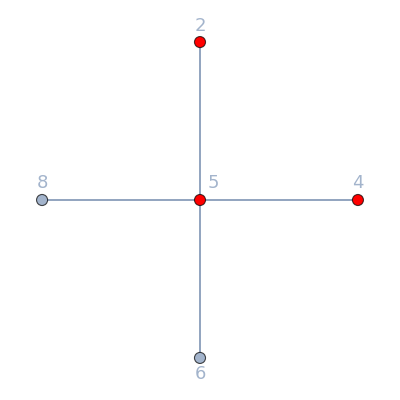

```mathematica
Graph[{3<-> 1, 2 <-> 1, 4 <-> 1, 5 <-> 1}, VertexLabels -> {1 -> 5, 2->Placed[4, Above],3 -> Placed[2,Above],4->Placed[6,Below], 5 -> Placed[8,Above]}, VertexLabelStyle->18, VertexStyle->{1|2|3->Red}, VertexCoordinates->{{0,1},{0,0},{1,0}, {0,-1},{-1,0}}, VertexSize->0.07]
```

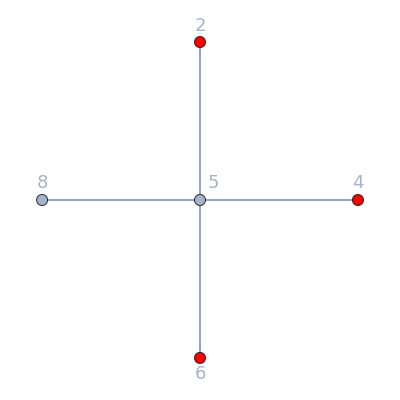

```mathematica
Graph[{3<-> 1, 2 <-> 1, 4 <-> 1, 5 <-> 1}, VertexLabels -> {1 -> 5, 2->Placed[4, Above],3 -> Placed[2,Above],4->Placed[6,Below], 5 -> Placed[8,Above]}, VertexLabelStyle->18, VertexStyle->{2|3|4->Red}, VertexCoordinates->{{0,1},{0,0},{1,0}, {0,-1},{-1,0}}, VertexSize->0.07]
```

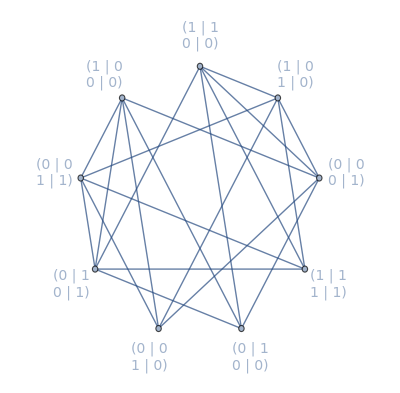

```mathematica
p = {{{1,0},{0,0}}//MatrixForm,{{0,0},{1,1}}//MatrixForm, {{0,1},{0,1}}//MatrixForm, {{0,0},{1,0}}//MatrixForm, {{0,1},{0,0}}//MatrixForm, {{1,1},{1,1}}//MatrixForm, {{0,0},{0,1}}//MatrixForm, {{1,0},{1,0}}//MatrixForm,{{1,1},{0,0}}//MatrixForm};
postavi = {Above,Above,"RadialOutside",Below,Below,Below,Below,Below,Below};
f = Graph[{1 <-> 2, 1 <-> 3, 1<-> 4,1 <-> 5, 2 <-> 6,1 <-> 7,2 <-> 3,2 <-> 4,2 <-> 8, 3 <-> 5,3 <-> 6,3 <-> 9,4<-> 7,4<-> 8, 5<-> 9,5<-> 7, 6<-> 8, 6<-> 9, 7<-> 8,7<-> 9, 8<-> 9},  VertexLabelStyle->14, GraphLayout->{"CircularEmbedding","OptimalOrder"->False}, VertexLabels->"Name"];
vc = GraphEmbedding[f];
c  = Table[.5+1.6Pi vc[[i]],{i,9}];
a = Thread[VertexList[f]->Table[Placed[Part[p,i],Part[c,i]] ,{i,9}]];
Graph[f,VertexLabels->a]
```